# Supporting Information Sec 3.6 Squares

```mathematica
Import["ToMatlab.m","Package"]
```

## AA stacking Eq. S19

```mathematica
ClearAll["Global`*"]
```

```mathematica
fAA[x_,y_,λ_]=  (Cos[(4 π x)/(√3 λ)]+2 Cos[(2  π x)/(√3 λ)] Cos[(2  π y)/λ])
```

Cos[(4 π x)/(√3 λ)]+2 Cos[(2 π x)/(√3 λ)] Cos[(2 π y)/λ]

```mathematica
Plot3D[fAA[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
λ0=as/(2*(1-Cos[θ]))^(1/2)
```

as/(√2 √(1-Cos[θ]))

```mathematica
f0AA[x_,y_,as_,θ_]=fAA[x,y,λ0]
```

Cos[(4 √(2/3) π x √(1-Cos[θ]))/as]+2 Cos[(2 √(2/3) π x √(1-Cos[θ]))/as] Cos[(2 √2 π y √(1-Cos[θ]))/as]

```mathematica
nRf0AA[x_,y_,as_,θ_,R_]=f0AA[x R,y R,as,θ]
```

Cos[(4 √(2/3) π R x √(1-Cos[θ]))/as]+2 Cos[(2 √(2/3) π R x √(1-Cos[θ]))/as] Cos[(2 √2 π R y √(1-Cos[θ]))/as]

```mathematica
nRnasf0AA[x_,y_,as_,θ_,r_]=nRf0AA[x,y,as,θ,r*as]
```

Cos[4 √(2/3) π r x √(1-Cos[θ])]+2 Cos[2 √(2/3) π r x √(1-Cos[θ])] Cos[2 √2 π r y √(1-Cos[θ])]

```mathematica
nRnasnareauf0AA[x_,y_,θ_,r_]=nRnasf0AA[x,y,as,θ,r]
```

Cos[4 √(2/3) π r x √(1-Cos[θ])]+2 Cos[2 √(2/3) π r x √(1-Cos[θ])] Cos[2 √2 π r y √(1-Cos[θ])]

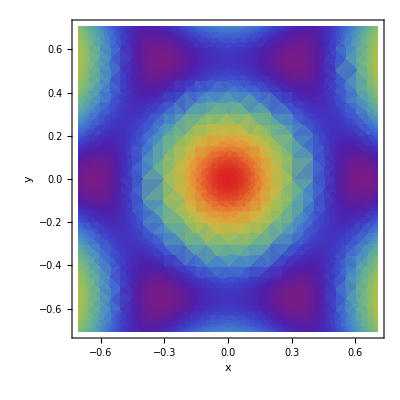

```mathematica
DensityPlot[nRnasnareauf0AA[x,y,3/180*Pi,10Sqrt[3]],{x,-(√2)/2,(√2)/2},{y,-(√2)/2,(√2)/2},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},y<(√2)/2 &&y>-(√2)/2 && x>-(√2)/2 &&x<(√2)/2],AspectRatio->Automatic]
```

```mathematica
t1=AbsoluteTime[];
squareAA[θ_,r_]=FullSimplify[Integrate[nRnasnareauf0AA[x,y,θ,r]Boole[y<(√2)/2 &&y>-(√2)/2 && x>-(√2)/2 &&x<(√2)/2 ],{x,-(√2)/2,(√2)/2},{y,-(√2)/2,(√2)/2}] ]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins" ]
```

(√3 (Csc[θ/2]^2 Sin[2 π r √(1-Cos[θ])] Sin[(2 π r √(1-Cos[θ]))/(√3)]+(π r Sin[(4 π r √(1-Cos[θ]))/(√3)])/(√(1-Cos[θ]))))/(2 π^2 r^2)

time used 0.093519165 mins

```mathematica
ToMatlab[squareAA[theta,r]]
```

(1/2).*3.^(1/2).*pi.^(-2).*r.^(-2).*(csc((1/2).*theta).^2.*sin(2.* ...
  pi.*r.*(1+(-1).*cos(theta)).^(1/2)).*sin(2.*3.^(-1/2).*pi.*r.*(1+( ...
  -1).*cos(theta)).^(1/2))+pi.*r.*(1+(-1).*cos(theta)).^(-1/2).*sin( ...
  4.*3.^(-1/2).*pi.*r.*(1+(-1).*cos(theta)).^(1/2)));

## AB stacking Eq. S20

```mathematica
fAB[x_,y_,λ_]=  Cos[(4 π (x-λ/√3))/(√3 λ)]+2 Cos[(2  π (x-λ/√3))/(√3 λ)] Cos[(2  π y)/λ]
```

2 Cos[(2 π y)/λ] Cos[(2 π (x-λ/(√3)))/(√3 λ)]+Cos[(4 π (x-λ/(√3)))/(√3 λ)]

```mathematica
Plot3D[fAB[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
λ0=as/(2*(1-Cos[θ]))^(1/2)
```

as/(√2 √(1-Cos[θ]))

```mathematica
f0AB[x_,y_,as_,θ_]=fAB[x,y,λ0]
```

2 Cos[(2 √2 π y √(1-Cos[θ]))/as] Cos[(2 √(2/3) π (x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]+Cos[(4 √(2/3) π (x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]

```mathematica
nRf0AB[x_,y_,as_,θ_,R_]=f0AB[x R,y R,as,θ]
```

2 Cos[(2 √2 π R y √(1-Cos[θ]))/as] Cos[(2 √(2/3) π (R x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]+Cos[(4 √(2/3) π (R x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]

```mathematica
nRnasf0AB[x_,y_,as_,θ_,r_]=nRf0AB[x,y,as,θ,r*as]
```

2 Cos[2 √2 π r y √(1-Cos[θ])] Cos[(2 √(2/3) π (as r x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]+Cos[(4 √(2/3) π (as r x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]

```mathematica
nRnasnareauf0AB[x_,y_,θ_,r_]=nRnasf0AB[x,y,as,θ,r]
```

2 Cos[2 √2 π r y √(1-Cos[θ])] Cos[(2 √(2/3) π (as r x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]+Cos[(4 √(2/3) π (as r x-as/(√6 √(1-Cos[θ]))) √(1-Cos[θ]))/as]

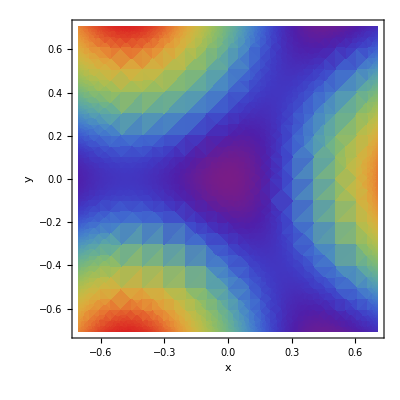

```mathematica
DensityPlot[nRnasnareauf0AB[x,y,2/180*Pi,10Sqrt[3]],{x,-(√2)/2,(√2)/2},{y,-(√2)/2,(√2)/2},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},y<(√2)/2 &&y>-(√2)/2 && x>-(√2)/2 &&x<(√2)/2],AspectRatio->Automatic]
```

```mathematica
t1=AbsoluteTime[];
squareAB[θ_,r_]=FullSimplify[Integrate[nRnasnareauf0AB[x,y,θ,r]Boole[y<(√2)/2 &&y>-(√2)/2 && x>-(√2)/2 &&x<(√2)/2 ],{x,-(√2)/2,(√2)/2},{y,-(√2)/2,(√2)/2}] ]
t2=AbsoluteTime[];
```

-(√3 (Csc[θ/2]^2 Sin[2 π r √(1-Cos[θ])] Sin[(2 π r √(1-Cos[θ]))/(√3)]+(π r Sin[(4 π r √(1-Cos[θ]))/(√3)])/(√(1-Cos[θ]))))/(4 π^2 r^2)

```mathematica
ToMatlab[squareAB[theta,r]]
```

(-1/4).*3.^(1/2).*pi.^(-2).*r.^(-2).*(csc((1/2).*theta).^2.*sin( ...
  2.*pi.*r.*(1+(-1).*cos(theta)).^(1/2)).*sin(2.*3.^(-1/2).*pi.*r.*( ...
  1+(-1).*cos(theta)).^(1/2))+pi.*r.*(1+(-1).*cos(theta)).^(-1/2).* ...
  sin(4.*3.^(-1/2).*pi.*r.*(1+(-1).*cos(theta)).^(1/2)));